```mathematica
(* Broadband pulses with fixed profile bandwidths ϵ = 0.2, 0.3, 0.4, ... *)
(* Minimized total pulse area ≤ 5π *)
(* Target probability: p = 1, 1/2, 1/4 *)
(* Error < 10^-2 *)
```

```mathematica
plotUtils=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"plot_utils.m"}];
<<(plotUtils)
```

```mathematica
root=rootBB;
err=0.01;
error=", error="<>ToString@err;
totalArea[rule_,npulses_]:=Module[{vars=rule/.Rule[a_,b_]->a},npulses Abs[vars[[-1]]/.rule]];
```

BB3; p=1, error=0.01

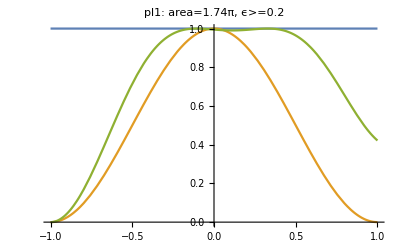

BB3; p=1/2, error=0.01

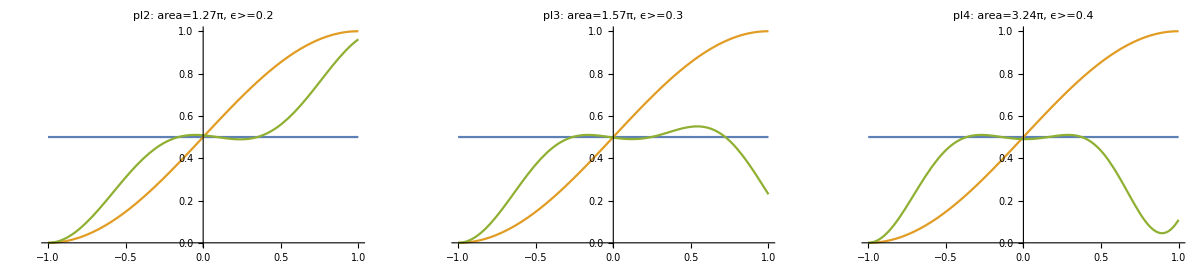

BB3; p=1/4, error=0.01

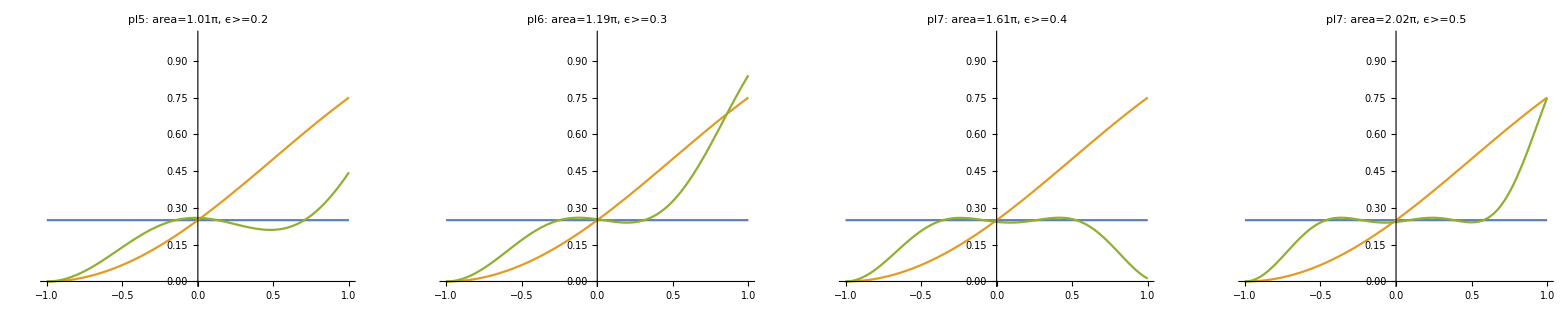

```mathematica
(*N=3 - Same areas as with different Rabi. However, different Rabi provide higher BW. Can't find width=0.3, 0.4 for pop=1.0*)
sequence=U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
sequenceS=U[-Δ1,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
pltN[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label, totalArea[rule,3]]
pltS[p_,rule_,label_]:=plot[p,err,sequenceS,rule,p,label, totalArea[rule,3]]

pl1=pltS[1,{Δ1->0.6718,Δ2->0 ,Ω1->0.57895},"pl1"];

pl2=pltN[1/2,{Δ1->-0.2282,Δ2->0.3812,Δ3->0.642,Ω1->0.4218},"pl2"];
pl3=pltN[1/2,{Δ1->0.1745,Δ2->0.1253,Δ3->0.9254,Ω1->0.5218},"pl3"];
pl4=pltN[1/2,{Δ1->0.9154,Δ2->-5.0992,Δ3->0.0526,Ω1->1.0794},"pl4"];

pl5=pltN[1/4,{Δ1->-0.1186,Δ2->0.5508,Δ3->0.5073,Ω1->0.3370},"pl5"];
pl6=pltN[1/4,{Δ1->0.5654,Δ2->0.5328,Δ3->-0.1098,Ω1->0.397},"pl6"];
pl7=pltN[1/4,{Δ1->0.9873,Δ2->0.1511,Δ3->0.4675,Ω1->0.5377},"pl7"];
pl8=pltN[1/4,{Δ1->-0.5145,Δ2->-0.8088,Δ3->0.7947,Ω1->0.6719},"pl7"];

GGrid[Text[Style["BB3; p=1"<> error,FontSize->20]],{{pl1,Null,Null,Null}},ImageSize->Full]
GGrid[Text[Style["BB3; p=1/2"<> error,FontSize->20]],{{pl2,pl3,pl4,Null}},ImageSize->Full]
GGrid[Text[Style["BB3; p=1/4"<> error,FontSize->20]],{{pl5,pl6,pl7,pl8}},ImageSize->Full]
```

```mathematica
(*N=4, 5 DO NOT OFFER SMALLER PULSE AREAS THAN N=3 - however larger bandwidhts can be obtained*)
```

BB4; p=1, error=0.01

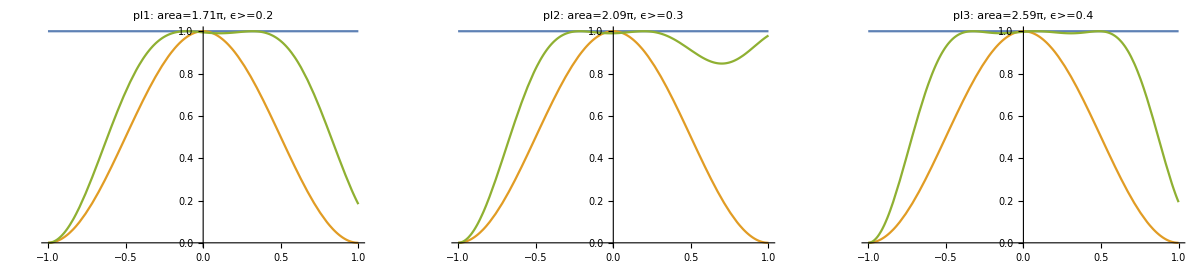

BB4; p=1/2, error=0.01

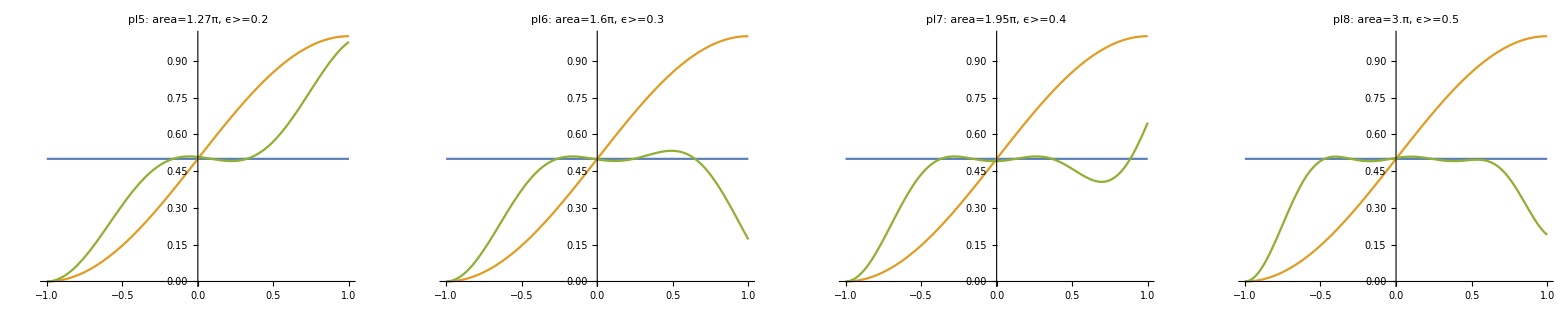

BB4; p=1/4, error=0.01

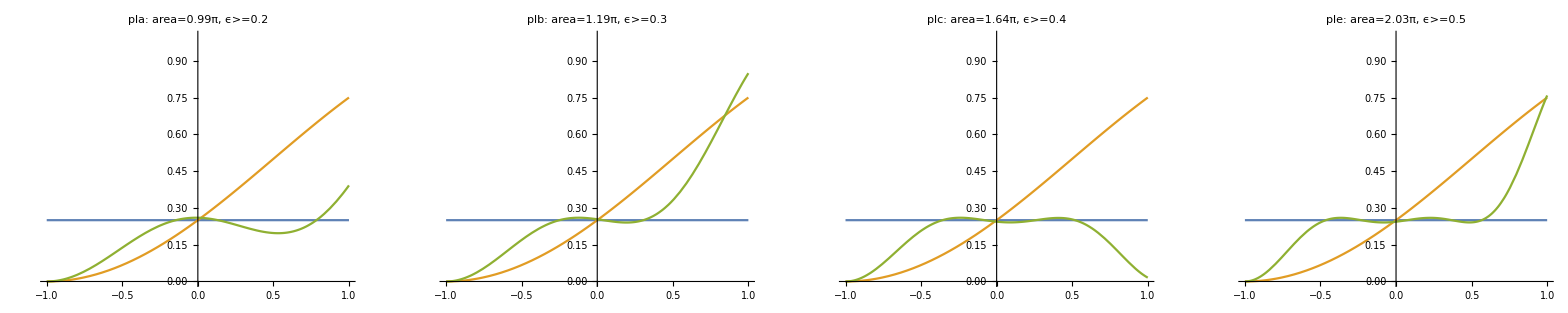

```mathematica
(*N=4 - Same area as with different Rabi. However, different Rabi provide larger BW. Can't not find width=0.5 for pop=1.0*)
(*Choose this*)
sequence=U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
sequenceS=U[-Δ1,Ω1].U[-Δ2,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
pltN[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label,totalArea[rule,4]]
pltS[p_,rule_,label_]:=plot[p,err,sequenceS,rule,p,label,totalArea[rule,4]]

pl1=pltS[1,{Δ1->0.3125,Δ2->0.4409,Ω1->0.4274},"pl1"];
pl2=pltS[1,{Δ1->-0.0673,Δ2->-0.7162,Ω1->0.5224},"pl2"];
pl3=pltS[1,{Δ1->0.8280,Δ2->-0.0138,Ω1->0.6472},"pl3"];

pl5=pltN[1/2,{Δ1->0.4296,Δ2->0.4537,Δ3->0.0387,Δ4->-0.1196,Ω1->0.3167},"pl5"];
pl6=pltN[1/2,{Δ1->0.7650,Δ2->0.3372,Δ3->-0.0551,Δ4->0.3031,Ω1->0.4008},"pl6"];
pl7=pltN[1/2,{Δ1->-0.0165,Δ2->0.2309,Δ3->0.1818,Δ4->0.9427,Ω1->0.4884},"pl7"];
pl8=pltN[1/2,{Δ1->0.5808,Δ2->-0.3101,Δ3->-2.7331,Δ4->0.4131,Ω1->0.7501},"pl8"];

pla=pltN[1/4,{Δ1->0.0273,Δ2->0.1075,Δ3->0.5837,Δ4->0.1850,Ω1->0.2468},"pla"];
plb=pltN[1/4,{Δ1->0.3270,Δ2->0.5514,Δ3->0.0821,Δ4->0.0900,Ω1->0.2969},"plb"];
plc=pltN[1/4,{Δ1->0.8474,Δ2->0.3143,Δ3->0.0995,Δ4->0.4541,Ω1->0.4093},"plc"];
pld=pltN[1/4,{Δ1->0.9855,Δ2->0.1957,Δ3->0.3230,Δ4->0.1968,Ω1->0.5083},"ple"];

GGrid[Text[Style["BB4; p=1"<> error,FontSize->20]],{{pl1,pl2,pl3,Null}},ImageSize->Full]
GGrid[Text[Style["BB4; p=1/2"<> error,FontSize->20]],{{pl5,pl6,pl7,pl8}},ImageSize->Full]
GGrid[Text[Style["BB4; p=1/4"<> error,FontSize->20]],{{pla,plb,plc,pld}},ImageSize->Full]
```

BB5 p=1, error=0.01

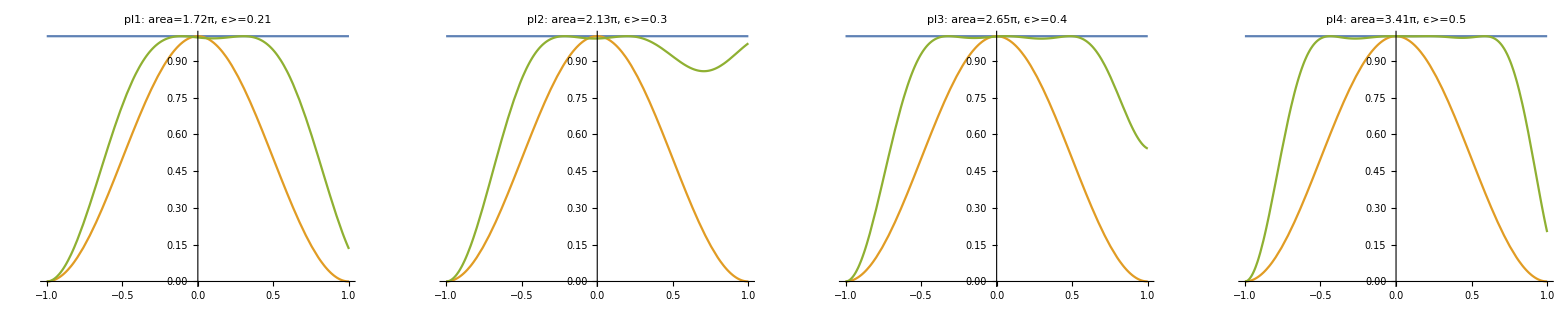

BB5 p=1/2, error=0.01

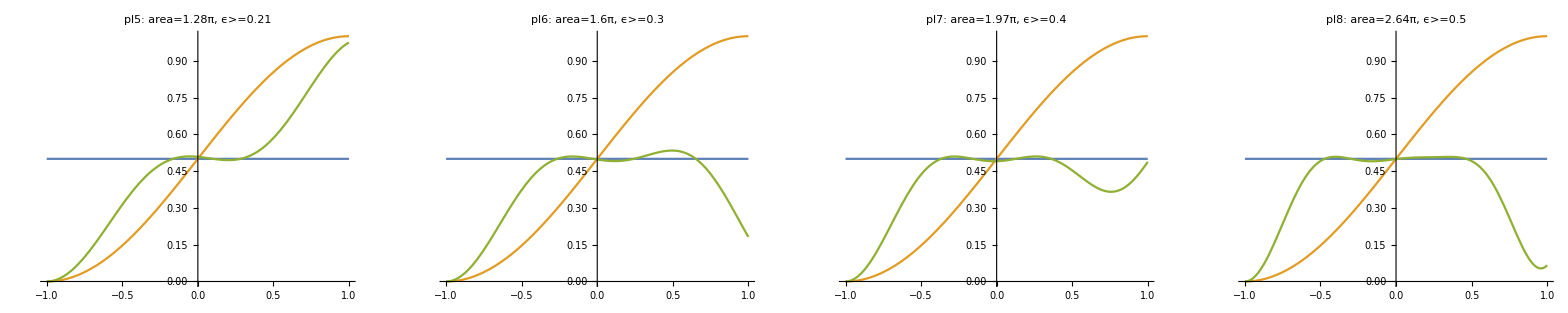

BB5 p=1/4, error=0.01

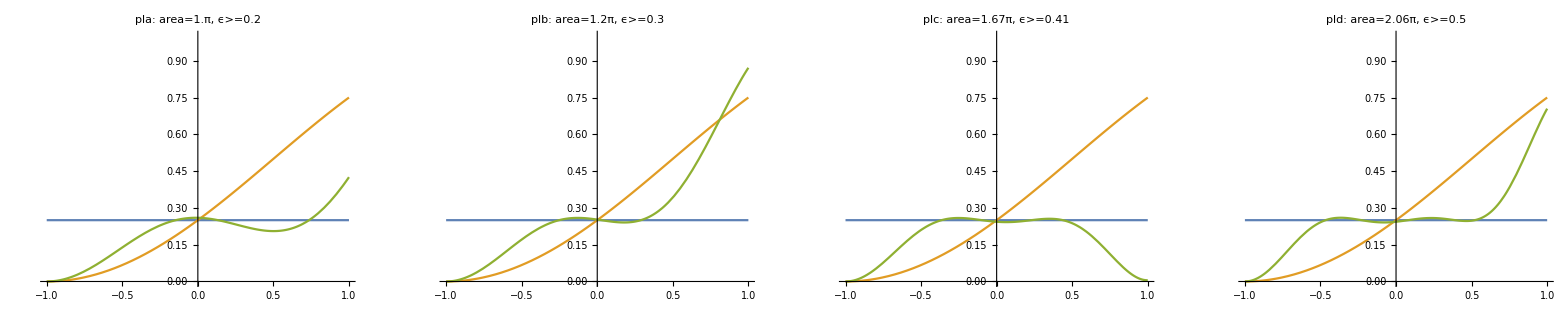

```mathematica
(*N=5 - Same total area. However, different Rabi probide BW=0.6*)
(*Choose this*)
sequenceS=U[-Δ1,Ω1].U[-Δ2,Ω1].U[0,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
sequence=U[Δ5,Ω1].U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
pltS[p_,rule_,label_]:=plot[p,err,sequenceS,rule,p,label, totalArea[rule,5]]
pltN[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label,totalArea[rule,5]]

pl1=pltS[1,{Δ1->0.1866,Δ2->0.4208,Ω1->0.3431},"pl1"];
pl2=pltS[1,{Δ1->0.2405,Δ2->-0.6853,Ω1->0.4263},"pl2"];
pl3=pltS[1,{Δ1->0.7886,Δ2->0.1210,Ω1->0.5305},"pl3"];
pl4=pltS[1,{Δ1->0.5315,Δ2->-0.8530,Ω1->0.6821},"pl4"];

pl5=pltN[1/2,{Δ1->0.0086,Δ2->-0.0250,Δ3->0.0939,Δ4->0.5440,Δ5->0.1674,Ω1->0.2560},"pl5"];
pl6=pltN[1/2,{Δ1->0.5979,Δ2->0.4223,Δ3->0.0406,Δ4->-0.0211,Δ5->0.3419,Ω1->0.3210},"pl6"];
pl7=pltN[1/2,{Δ1->0.0800,Δ2->0.0622,Δ3->0.2072,Δ4->0.24380,Δ5->0.8766,Ω1->0.3939},"pl7"];
pl8=pltN[1/2,{Δ1->1.0619,Δ2->0.1576,Δ3->0.3974,Δ4->-0.0906,Δ5->0.2440,Ω1->0.5273},"pl8"];

pla=pltN[1/4,{Δ1->0.0721,Δ2->0.0513,Δ3->0.2756,Δ4->0.3836,Δ5->0.2606,Ω1->0.1992},"pla"];
plb=pltN[1/4,{Δ1->0.1831,Δ2->0.4653,Δ3->0.2653,Δ4->0.0137,Δ5->0.0925,Ω1->0.2395},"plb"];
plc=pltN[1/4,{Δ1->0.1557,Δ2->0.3589,Δ3->-0.0733,Δ4->0.4891,Δ5->0.6372,Ω1->0.3343},"plc"];
pld=pltN[1/4,{Δ1->0.9012,Δ2->0.2882,Δ3->0.1816,Δ4->0.2595,Δ5->0.1408,Ω1->0.4121},"pld"];

GGrid[Text[Style["BB5 p=1"<> error,FontSize->20]],{{pl1,pl2,pl3,pl4}},ImageSize->Full]
GGrid[Text[Style["BB5 p=1/2"<> error,FontSize->20]],{{pl5,pl6,pl7,pl8}},ImageSize->Full]
GGrid[Text[Style["BB5 p=1/4"<> error,FontSize->20]],{{pla,plb,plc,pld}},ImageSize->Full]
```

BB6 p=1, error=0.01

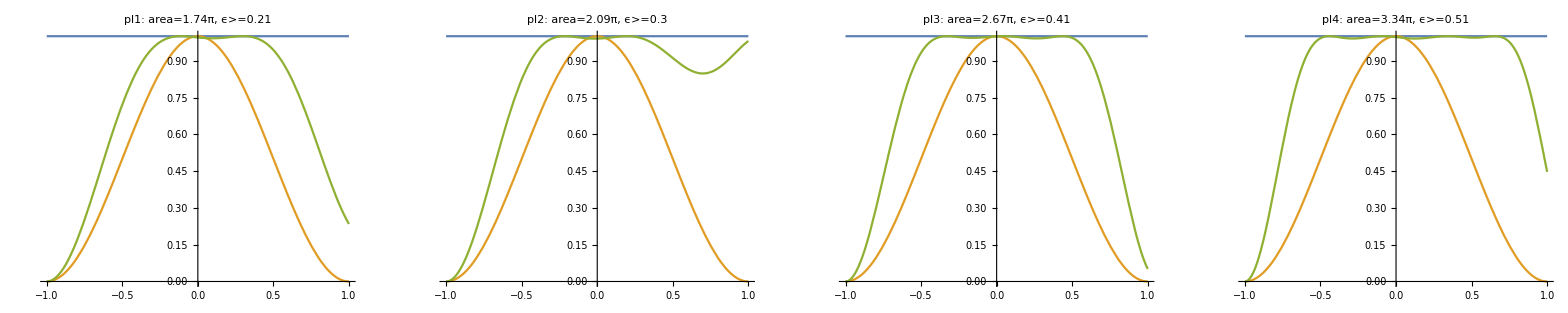

BB6 p=1/2, error=0.01

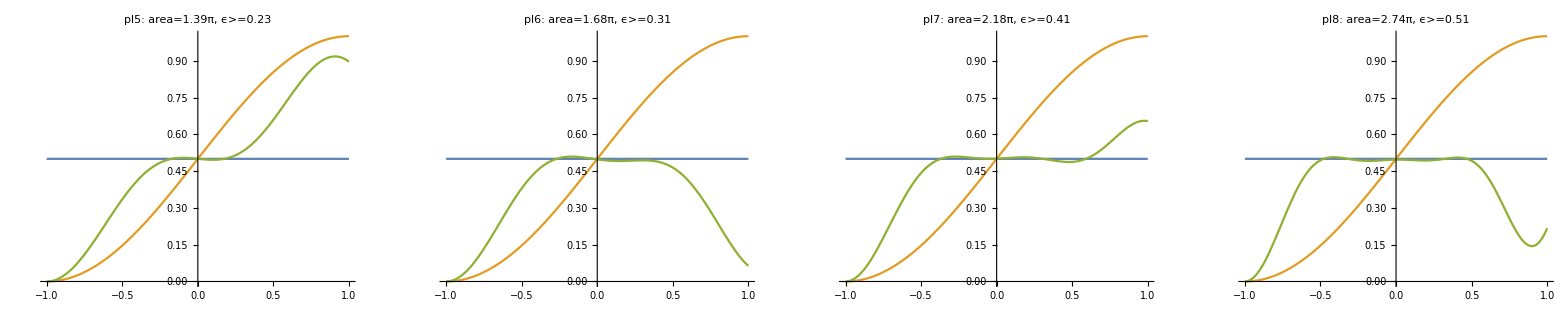

BB6 p=1/4, error=0.01

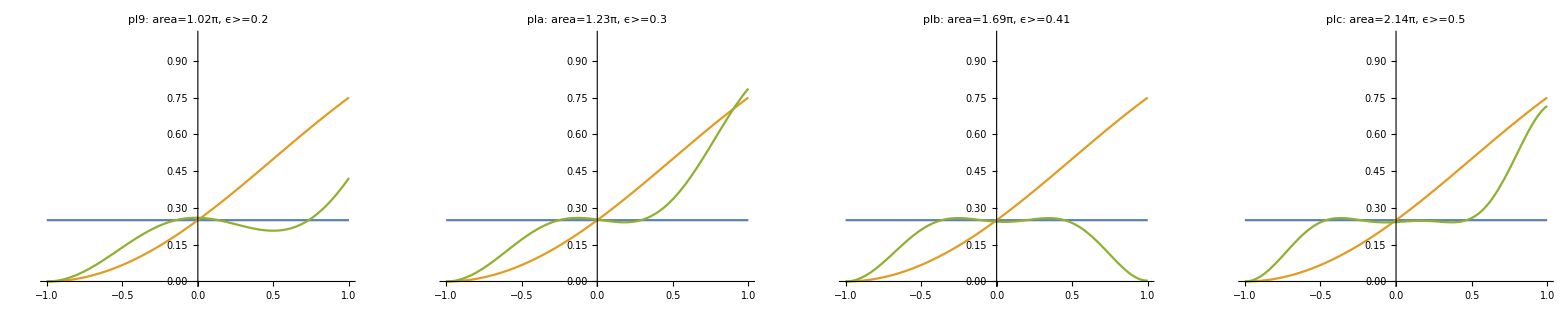

```mathematica
(*N=6 - NO USE, BB5 yield smaller areas and same BWs*)
sequenceS=U[-Δ1,Ω1].U[-Δ2,Ω1].U[-Δ3,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
sequence=U[Δ6,Ω1].U[Δ5,Ω1].U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
pltN[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label,totalArea[rule,6]]
pltS[p_,rule_,label_]:=plot[p,err,sequenceS,rule,p,label,totalArea[rule,6]]

pl1=pltS[1,{Δ1->0.1685,Δ2->0.4437,Δ3->-0.0588,Ω1->0.2908},"pl1"];
pl2=pltS[1,{Δ1->-0.0553,Δ2->0.2884,Δ3->0.5278,Ω1->0.3489},"pl2"];
pl3=pltS[1,{Δ1->0.6076,Δ2->0.3306,Δ3->-0.1668,Ω1->0.4444},"pl3"];
pl4=pltS[1,{Δ1->0.8594,Δ2->0.0932,Δ3->0.1626,Ω1->0.5571},"pl4"];

pl5=pltN[1/2,{Δ1->0.0725,Δ2->0.5121,Δ3->0.2025,Δ4->-0.0212,Δ5->-0.0073,Δ6->0.1298,Ω1->0.2309},"pl5"];
pl6=pltN[1/2,{Δ1->-0.0802,Δ2->-0.5250,Δ3->0.3095,Δ4->0.3284,Δ5->0.3442,Δ6->0.0910,Ω1->0.2806},"pl6"];
pl7=pltN[1/2,{Δ1->0.9218,Δ2->0.2700,Δ3->0.2377,Δ4->0.1229,Δ5->0.0969,Δ6->-0.0145,Ω1->0.3628},"pl7"];
pl8=pltN[1/2,{Δ1->0.9928,Δ2->0.2461,Δ3->0.2811,Δ4->0.1377,Δ5->0.03726,Δ6->0.0970,Ω1->0.4564},"pl8"];

pl9=pltN[1/4,{Δ1->0.3494,Δ2->0.1264,Δ3->0.5067,Δ4->-0.0196,Δ5->0.0038,Δ6->0.2746,Ω1->0.1701},"pl9"];
pla=pltN[1/4,{Δ1->0.0574,Δ2->0.0626,Δ3->0.1648,Δ4->0.2625,Δ5->0.2558,Δ6->0.4706,Ω1->0.2045},"pla"];
plb=pltN[1/4,{Δ1->0.3520,Δ2->0.1771,Δ3->0.0742,Δ4->0.1174,Δ5->0.4550,Δ6->0.5465,Ω1->0.2809},"plb"];
plc=pltN[1/4,{Δ1->0.1290,Δ2->0.1974,Δ3->0.1907,Δ4->0.1652,Δ5->0.3419,Δ6->0.8434,Ω1->0.3566},"plc"];

GGrid[Text[Style["BB6 p=1"<> error,FontSize->20]],{{pl1,pl2,pl3,pl4}},ImageSize->Full]
GGrid[Text[Style["BB6 p=1/2"<> error,FontSize->20]],{{pl5,pl6,pl7,pl8}},ImageSize->Full]
GGrid[Text[Style["BB6 p=1/4"<> error,FontSize->20]],{{pl9,pla,plb,plc}},ImageSize->Full]
```

BB7 p=1, error=0.01

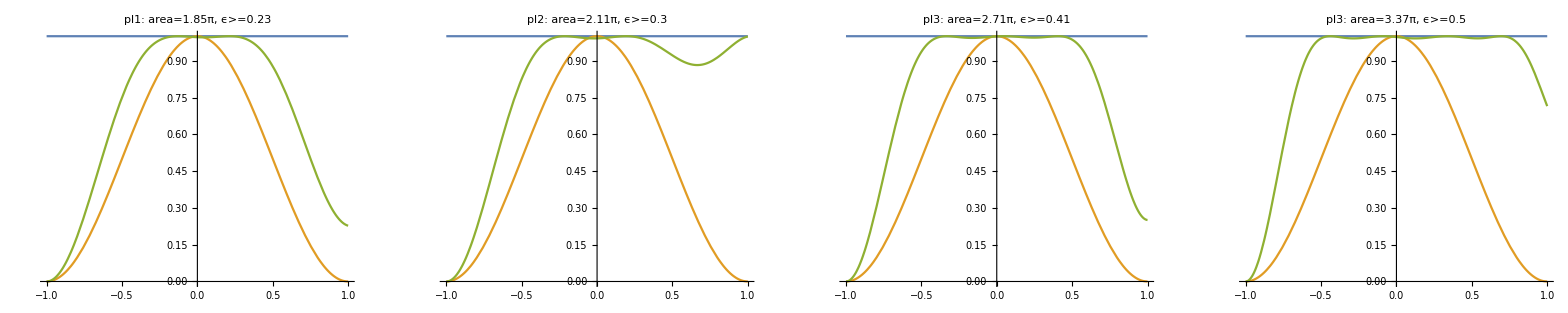

BB7 p=1/2, error=0.01

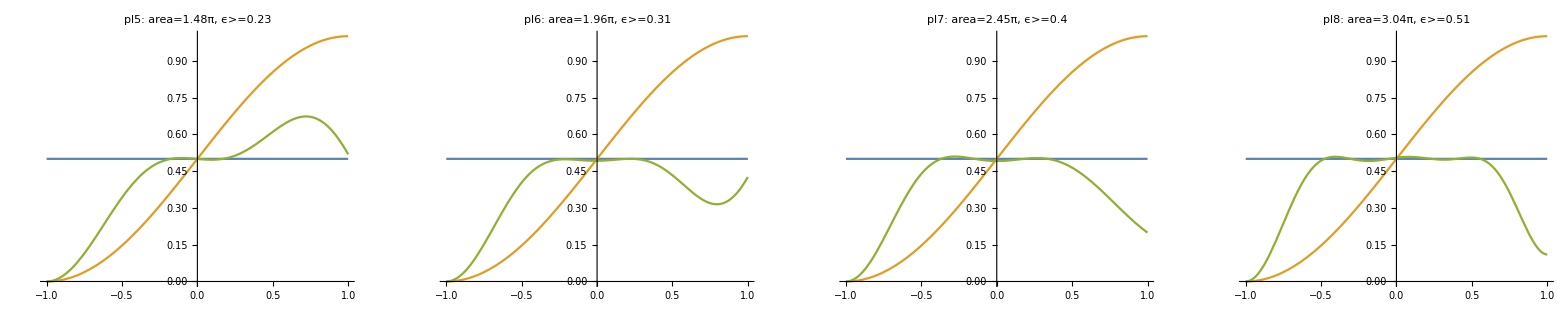

BB7 p=1/4, error=0.01

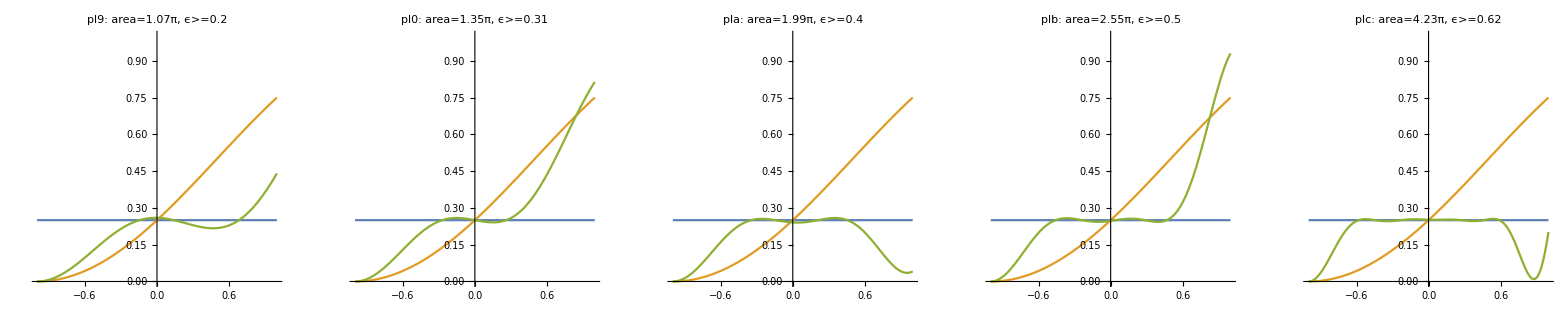

```mathematica
(*N=7 - NO USE, BB5 yield smaller areas and same BWs*)
sequence=U[Δ7,Ω1].U[Δ6,Ω1].U[Δ5,Ω1].U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
sequenceS=U[-Δ1,Ω1].U[-Δ2,Ω1].U[-Δ3,Ω1].U[0,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
pltN[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label,totalArea[rule,7]]
pltS[p_,rule_,label_]:=plot[p,err,sequenceS,rule,p,label,totalArea[rule,7]]

pl1=pltS[1,{Δ1->0.2861,Δ2->0.0407,Δ3->0.4428,Ω1->0.2647},"pl1"];
pl2=pltS[1,{Δ1->0.3883,Δ2->0.3887,Δ3->-0.0426,Ω1->0.3016},"pl2"];
pl3=pltS[1,{Δ1->0.5879,Δ2->0.3267,Δ3->-0.0193,Ω1->0.3867},"pl3"];
pl4=pltS[1,{Δ1->0.0881,Δ2->0.7786,Δ3->-0.3957,Ω1->0.4819},"pl3"];

pl5=pltN[1/2,{Δ1->0.0299,Δ2->0.6500,Δ3->-0.0189,Δ4->0.2468,Δ5->-0.1662,Δ6->0.2369,Δ7->-0.0597,Ω1->0.2118},"pl5"];
pl6=pltN[1/2,{Δ1->-0.1685,Δ2->0.6040,Δ3->-0.3494,Δ4->0.1194,Δ5->0.0447,Δ6->0.7815,Δ7->-0.1155,Ω1->0.2803},"pl6"];
pl7=pltN[1/2,{Δ1->0.3172,Δ2->0.0448,Δ3->0.6841,Δ4->0.3625,Δ5->-1.1427,Δ6->0.7058,Δ7->-0.4022,Ω1->0.3499},"pl7"];
pl8=pltN[1/2,{Δ1->1.8727,Δ2->0.8166,Δ3->0.0622,Δ4->-0.1130,Δ5->0.0756,Δ6->0.5013,Δ7->0.5086,Ω1->0.4340},"pl8"];

pl9=pltN[1/4,{Δ1->0.3685,Δ2->0.0013,Δ3->-0.0358,Δ4->0.1047,Δ5->0.5241,Δ6->0.2613,Δ7->-0.3189,Ω1->0.1528},"pl9"];
pl0=pltN[1/4,{Δ1->0.2998,Δ2->-0.1647,Δ3->0.7057,Δ4->0.1583,Δ5->-0.1115,Δ6->-0.1026,Δ7->0.5207,Ω1->0.1929},"pl0"];
pla=pltN[1/4,{Δ1->0.4707,Δ2->0.4990,Δ3->0.1108,Δ4->0.0909,Δ5->1.8147,Δ6->0.3376,Δ7->0.3191,Ω1->0.2837},"pla"];
plb=pltN[1/4,{Δ1->0.7814,Δ2->0.3810,Δ3->0.1057,Δ4->0.2048,Δ5->0.4463,Δ6->1.6228,Δ7->0.1643,Ω1->0.3642},"plb"];
plc=pltN[1/4,{Δ1->1.1109,Δ2->0.1673,Δ3->0.5282,Δ4->-0.1066,Δ5->1.1949,Δ6->1.1830,Δ7->-0.1318,Ω1->0.6037},"plc"];

GGrid[Text[Style["BB7 p=1"<> error,FontSize->20]],{{pl1,pl2,pl3,pl4,Null}},ImageSize->Full]
GGrid[Text[Style["BB7 p=1/2"<> error,FontSize->20]],{{pl5,pl6,pl7,pl8,Null}},ImageSize->Full]
GGrid[Text[Style["BB7 p=1/4"<> error,FontSize->20]],{{pl9,pl0,pla,plb,plc}},ImageSize->Full]
```